# Fourier cosine series expansion

```mathematica
Needs["FourierSeries`"]
```

```mathematica
Clear["Global`*"]
```

## Trigonometric representation

```mathematica
order=20;
```

```mathematica
f=UnitBox[2x/π];
```

```mathematica
fcs=FourierCosSeries[f,x,order]
```

1/4+(√2 Cos[x])/π+Cos[2 x]/π+(√2 Cos[3 x])/(3 π)-(√2 Cos[5 x])/(5 π)-Cos[6 x]/(3 π)-(√2 Cos[7 x])/(7 π)+(√2 Cos[9 x])/(9 π)+Cos[10 x]/(5 π)+(√2 Cos[11 x])/(11 π)-(√2 Cos[13 x])/(13 π)-Cos[14 x]/(7 π)-(√2 Cos[15 x])/(15 π)+(√2 Cos[17 x])/(17 π)+Cos[18 x]/(9 π)+(√2 Cos[19 x])/(19 π)

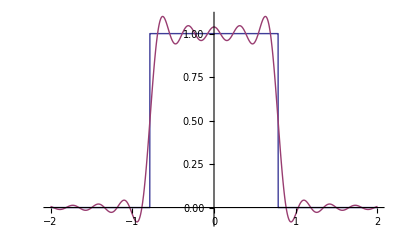

```mathematica
Plot[{f,fcs},{x,-2,2}]
```

### Fourier cosine coefficient

```mathematica
FourierCosCoefficient[f,x,n]
```

(2 Sin[(n π)/4])/(n π)

## Complex representation

```mathematica
fs=FourierSeries[f,x,order]
```

1/4+ⅇ^(-ⅈ x)/(√2 π)+ⅇ^(ⅈ x)/(√2 π)+ⅇ^(-2 ⅈ x)/(2 π)+ⅇ^(2 ⅈ x)/(2 π)+ⅇ^(-3 ⅈ x)/(3 √2 π)+ⅇ^(3 ⅈ x)/(3 √2 π)-ⅇ^(-5 ⅈ x)/(5 √2 π)-ⅇ^(5 ⅈ x)/(5 √2 π)-ⅇ^(-6 ⅈ x)/(6 π)-ⅇ^(6 ⅈ x)/(6 π)-ⅇ^(-7 ⅈ x)/(7 √2 π)-ⅇ^(7 ⅈ x)/(7 √2 π)+ⅇ^(-9 ⅈ x)/(9 √2 π)+ⅇ^(9 ⅈ x)/(9 √2 π)+ⅇ^(-10 ⅈ x)/(10 π)+ⅇ^(10 ⅈ x)/(10 π)+ⅇ^(-11 ⅈ x)/(11 √2 π)+ⅇ^(11 ⅈ x)/(11 √2 π)-ⅇ^(-13 ⅈ x)/(13 √2 π)-ⅇ^(13 ⅈ x)/(13 √2 π)-ⅇ^(-14 ⅈ x)/(14 π)-ⅇ^(14 ⅈ x)/(14 π)-ⅇ^(-15 ⅈ x)/(15 √2 π)-ⅇ^(15 ⅈ x)/(15 √2 π)+ⅇ^(-17 ⅈ x)/(17 √2 π)+ⅇ^(17 ⅈ x)/(17 √2 π)+ⅇ^(-18 ⅈ x)/(18 π)+ⅇ^(18 ⅈ x)/(18 π)+ⅇ^(-19 ⅈ x)/(19 √2 π)+ⅇ^(19 ⅈ x)/(19 √2 π)

```mathematica
Plot[{f,fs},{x,-2,2}]
```

-Graphics-

### Fourier Coefficient

```mathematica
FourierCoefficient[f,x,n]
```

Sin[(n π)/4]/(n π)